## S-matrix bootstrap: 2d

```mathematica
m = 1; (* Units of mass *)
Nmax = 30; (* Max exponent of rho in the expansion of S22. Typical value 30 *)
numberPoints =100; (* Choose the number of points on the s branch cut. Typical value 100*)
```

```mathematica
N2[s_]:=2Sqrt[s]Sqrt[s-4m^2];(* Denis (relativistic) normalization factor *)
```

```mathematica
(* rho-variable. This is Denis definition. *)
s0Choice=2m^2;
rhoOriginal=(Sqrt[4m^2-s0]-Sqrt[4m^2-s])/(Sqrt[4m^2-s0]+Sqrt[4m^2-s])/.s0->s0Choice;
rho=rhoOriginal/.Sqrt[4m^2-s]->-I Sqrt[s-4m^2];
rhoCrossed=rhoOriginal/.s->4m^2-s;
```

```mathematica
(* Denis way of generating the points. But just at MachinePrecision. *)
solutionS=Quiet[Solve[rhoOriginal==Exp[I ϕ],s]]//Flatten//FullSimplify;
sFromϕ=s/.solutionS;
(* Chebyshev distribution of n points in the interval [a,b] *)
chebyshevGrid[n_][a_,b_]:=(a+b)/2+(b-a)/2 Table[Cos[(2k-1)/(2n) π],{k,n,1,-1}];
(* we impose unitarity for a descrete numberPoints for s>=4m^2 *)
(* it is convenient to choose these points using the ϕ-variable and then transalte them to the s-variable *)
samplePhi    = chebyshevGrid[numberPoints][0,π];
points       = Table[sFromϕ,{ϕ,samplePhi}]//N;
```

```mathematica
(* Turn the 1x1 S matrix into a 2x2 Hermitian matrix. In Mathematica we can work with complex quantities. *)
elT[n_]:=1/; n==0;  
elT[n_] :=rho^n+rhoCrossed^n /; n>0;  
matrix={{1,1},{1,1}}+Sum[a[n]({{0, -I  elT[n]*},{I elT[n],0}} ),{n,0,Nmax}]/N2[s];
nummatrix=Table[matrix(\[VectorGreaterEqual])_2 0,{s,points}];
```

```mathematica
vars = Table[a[n],{n,0,Nmax}]; (* List of variables. (I set β=1 from the start) *)
```

```mathematica
(* Example 1: Minimize Λ0 *)
```

```mathematica
soluz=SemidefiniteOptimization[a[0],nummatrix, vars]
```

{a[0]→-7.95026,a[1]→50.5275,a[2]→-69.447,a[3]→79.4258,a[4]→-83.7272,a[5]→84.2214,a[6]→-82.1135,a[7]→78.2382,a[8]→-73.1953,a[9]→67.4253,a[10]→-61.2577,a[11]→54.9431,a[12]→-48.6733,a[13]→42.5902,a[14]→-36.7944,a[15]→31.3566,a[16]→-26.3294,a[17]→21.7537,a[18]→-17.6581,a[19]→14.0542,a[20]→-10.9372,a[21]→8.29019,a[22]→-6.08994,a[23]→4.30935,a[24]→-2.91367,a[25]→1.85953,a[26]→-1.09778,a[27]→0.578612,a[28]→-0.255879,a[29]→0.0843787,a[30]→-0.0153314}

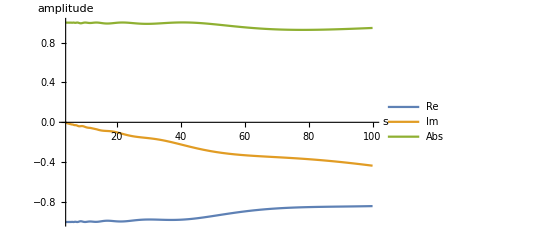

```mathematica
scat[s_] := 1+ I Sum[a[n]elT[n]/N2[s]/.soluz, {n,0,Nmax}];
Plot[{Re[scat[s]],Im[scat[s]],Abs[scat[s]]},{s,4,100},AxesLabel->{"s","amplitude"},PlotLegends->{"Re","Im","Abs"}]
```

```mathematica
(* Example 2: Find range of Λ2 as a function of Λ0. I generate 20 (lower) + 20 (upper) points.

NB: If you remove //Quiet you see that some points only give "Partial Success", see Mathematica manual.  *)
```

```mathematica
Do[a[0]=-7.95(21-iter)/20; soluzspanplus[iter]=SemidefiniteOptimization[(a[1]/8 +a[2]/16),nummatrix, Drop[vars,1]],{iter, 1, 20}]//Quiet;
Do[a[0]=-7.95(21-iter)/20; soluzspanminus[iter]=SemidefiniteOptimization[-(a[1]/8 +a[2]/16),nummatrix, Drop[vars,1]],{iter, 1, 20}]//Quiet;
a[0]=.;
```

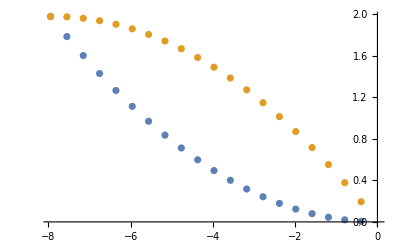

```mathematica
ListPlot[{Table[{-7.95(21-iter)/20,(a[1]/8 +a[2]/16)/.soluzspanplus[iter]},{iter, 1, 20}],Table[{-7.95(21-iter)/20,(a[1]/8 +a[2]/16)/.soluzspanminus[iter]},{iter, 1, 20}]}]
```